```mathematica
Clear["Global`"]
```

```mathematica
U={22,24,26,28,30};
```

```mathematica
λ={54.8,49.7,46.4,42.9,39.9};
```

```mathematica
x=1/U
```

{1/22,1/24,1/26,1/28,1/30}

```mathematica
y=λ
```

{54.8,49.7,46.4,42.9,39.9}

term in Var(x):

```mathematica
d=Sum[(x[[i]]-Mean[x])^2,{i,Length[x]}]
```

829133/9018009000

term in Cov(x,y):

```mathematica
e= Sum[(x[[i]]-Mean[x])y[[i]],{i,Length[x]}]
```

0.111477

term in Var(y):

```mathematica
f= Sum[(y[[i]]-Mean[y])^2,{i,Length[y]}]
```

135.372

slope of least squares line (nearly Corr(x,y)) and error:

```mathematica
m=e/d
```

1212.47

```mathematica
dm=Sqrt[(1/(Length[x]-2))(d f - e^2)/(d^2)]
```

27.5132

y - intercept of least squares line and error:

```mathematica
c=Mean[y]-m Mean[x]
```

-0.456857

```mathematica
dc=Sqrt[(1/(Length[x]-2))((d/Length[x])+Mean[x]^2)(d f -e^2)/(d^2)]
```

1.07746

least squares line through origin:

```mathematica
m0=Sum[x[[i]]y[[i]],{i,Length[x]}]/Sum[x[[i]]^2,{i,Length[x]}]
```

1200.88

```mathematica
dm0=Sqrt[Sum[(y[[i]]-m0 x[[i]])^2,{i,Length[x]}]/((Length[x]-1)Sum[x[[i]],{i,Length[x]}])]
```

0.533165

extra analysis:

```mathematica
A=m 10^-9
```

1.21247×10^-6

```mathematica
dA=dm 10^-9
```

2.75132×10^-8

```mathematica
speedLight=299792458
```

299792458

```mathematica
funCharge=1.6021766208 10^-19
```

1.60218×10^-19

```mathematica
dfunCharge=0.0000000098 10^-19
```

9.8×10^-28

```mathematica
h=(funCharge/speedLight)A
```

6.47981×10^-34

```mathematica
dh = Sqrt[((funCharge/speedLight)dA)^2 +((A/speedLight) dfunCharge)^2]
```

1.47038×10^-35

```mathematica
Sqrt[((funCharge/speedLight)dA)^2]
```

1.47038×10^-35

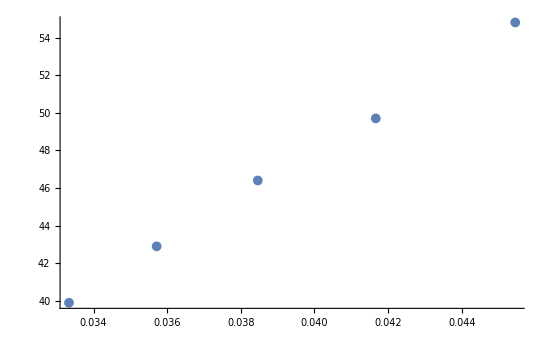

```mathematica
ListPlot[Table[{x[[i]],y[[i]]},{i,Length[x]}],PlotStyle->"Scientific"]
```

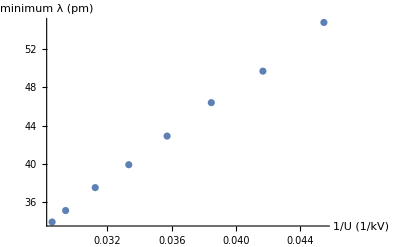

```mathematica
Show[%362,AxesLabel->{HoldForm["1/U (1/kV)"],HoldForm["minimum λ (pm)"]},PlotLabel->None,PlotStyle->"Scientific"]
```